Se presenta gráficas de los índices de refracción de datos experimentales obtenidos de https://refractiveindex.info/ para diversos materiales

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
c=3*^17 ;(*nm s^-1*)
```

```mathematica
Needs["MaTeX`"]
```

### Oro

```mathematica
au=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Oro Johnson.csv"];
```

```mathematica
nau1=Drop[Drop[au,{51,101}],1];
kau1=Drop[au,{1,52}];
λAu=nau1[[All,1]]*1000; (*λ en um*)
ℏωAu=h c/λAu; (*eV*)
nau=nau1[[All,2]];
kAu=kau1[[All,2]];
nAu=nau+ I kAu;
```

```mathematica
λAu
```

{187.9,191.6,195.3,199.3,203.3,207.3,211.9,216.4,221.4,226.2,231.3,237.1,242.6,249.,255.1,261.6,268.9,276.1,284.4,292.4,300.9,310.7,320.4,331.5,342.5,354.2,367.9,381.5,397.4,413.3,430.5,450.9,471.4,495.9,520.9,548.6,582.1,616.8,659.5,704.5,756.,821.1,892.,984.,1088.,1216.,1393.,1610.,1937.}

```mathematica
ℏωAu
```

{6.60298,6.47547,6.35279,6.22529,6.10281,5.98505,5.85512,5.73337,5.60389,5.48497,5.36403,5.23281,5.11418,4.98273,4.86358,4.74274,4.61398,4.49366,4.36252,4.24316,4.1233,3.99324,3.87235,3.74269,3.62248,3.50282,3.37238,3.25216,3.12204,3.00194,2.882,2.75161,2.63195,2.50192,2.38184,2.26158,2.13142,2.01151,1.88127,1.76111,1.64114,1.51102,1.39092,1.26087,1.14035,1.02031,0.890668,0.770621,0.640527}

```mathematica
hbarraomegaAu=Drop[ℏωAu,{1,2}];
epsReal=Re[Drop[nAu,{1,2}]^2];
epsImag=Im[Drop[nAu,{1,2}]^2];
```

```mathematica
auReal = Interpolation[Transpose[{hbarraomegaAu,epsReal}]];
auImag = Interpolation[Transpose[{hbarraomegaAu,epsImag}]];
```

```mathematica
nAu[[1]]^2
epsReal[[1]]
epsImag[[1]]
```

0.227056+3.04128 ⅈ

0.227056

3.04128

```mathematica
h c/2.5
```

496.28

```mathematica
upperTicks4=Module[{labels,positions},labels={310,355,414,496,620,827,1240};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor4=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

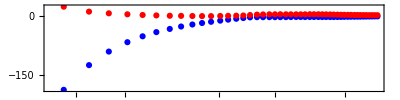

```mathematica
drudeAu=ListLogLinearPlot[{Style[auReal ,Blue],Style[auImag,Red]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],
FrameLabel->{{Style[MaTeX["\mbox{Re}[\epsilon (\omega)] "],Magnification->1.2],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.2],None}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{All,None},{Automatic,None}},PlotRange->All,AspectRatio->1/4]
```

```mathematica
Export["drudeAu.svg",drudeAu]
```

drudeAu.svg

### Plata

Datos obtenidos de Rakic.b4  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
ag=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Plata Johnson.csv"];
```

```mathematica
nag1=Drop[Drop[ag,{51,101}],1];
kag1=Drop[ag,{1,52}];
λAg=nag1[[All,1]]*1000;(*λ en um*)
ℏωAg=h c/λAg; (*eV*)
nAg=nag1[[All,2]];
kAg=kag1[[All,2]];
nAgg=nAg+ I kAg;
plata=Transpose[{λAg,nAgg}];
```

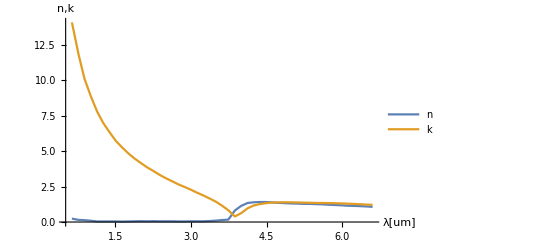

```mathematica
ListLinePlot[{Transpose[{ℏωAg,nAg}],Transpose[{ℏωAg,kAg}]},PlotRange->All,AxesLabel->{"λ[um]","n,k"},PlotLegends->{"n","k"}]
```

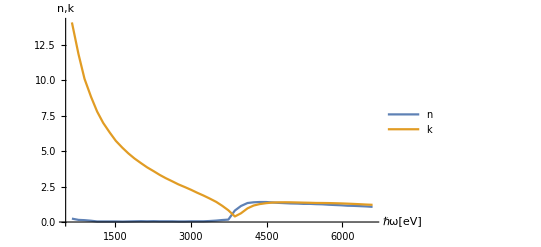

```mathematica
ListLinePlot[{Transpose[{ℏωAg,nAg}],Transpose[{ℏωAg,kAg}]},PlotRange->All,AxesLabel->{"ℏω[eV]","n,k"},PlotLegends->{"n","k"}]
```

### Bismuto

Datos obtenidos de Hagemann  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
bism=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Bismuto Hagemann.csv"];
```

```mathematica
nbism1=Drop[Drop[bism,{152,303}],1];
kbism1=Drop[bism,{1,153}];
λBism=nbism1[[All,1]]*100;(*λ en um*)
ℏωBism=h c/λBism; (*eV*)
nBis=nbism1[[All,2]];
kBis=kbism1[[All,2]];
nBismuto=nBis+ I kBis;
bismuto=Transpose[{λBism,nBismuto}];
```

```mathematica
λBism
```

{0.000248,0.0004133,0.00124,0.001378,0.001459,0.00248,0.004133,0.006199,0.008266,0.008856,0.009537,0.01033,0.0124,0.0155,0.02066,0.031,0.03542,0.03757,0.03875,0.03999,0.04133,0.04428,0.04769,0.04959,0.05061,0.05166,0.05636,0.06199,0.06888,0.07749,0.08856,0.09537,0.1033,0.1127,0.124,0.1305,0.1378,0.1459,0.155,0.1653,0.1771,0.1907,0.2066,0.2254,0.248,0.2583,0.2695,0.2818,0.2952,0.31,0.3179,0.3263,0.3351,0.3444,0.3542,0.3647,0.3757,0.3875,0.3999,0.4133,0.4275,0.4428,0.4592,0.4769,0.4959,0.5166,0.5391,0.5636,0.5904,0.6199,0.6525,0.6888,0.7293,0.7749,0.8266,0.8551,0.8856,0.9184,0.9537,0.9919,1.033,1.078,1.127,1.181,1.24,1.305,1.378,1.459,1.55,1.653,1.771,1.907,2.066,2.101,2.138,2.175,2.214,2.254,2.296,2.339,2.384,2.431,2.48,2.583,2.695,2.818,2.952,3.1,3.263,3.444,3.647,3.757,3.875,3.999,4.133,4.203,4.275,4.35,4.428,4.509,4.592,4.679,4.769,4.862,4.959,5.061,5.166,5.276,5.391,5.636,6.199,6.888,7.749,8.856,10.33,12.4,15.5,20.66,24.8,31.,35.42,41.33,49.59,61.99,82.66,124.,155.,206.6,310.,619.9}

```mathematica
hbarraomegaBi=Drop[Drop[ℏωBism,{1,136}],{14}];
epsRealBi=Drop[Re[Drop[nBismuto,{1,136}]^2],{14}];
epsImagBi=Drop[Im[Drop[nBismuto,{1,136}]^2],{14}];
```

```mathematica
biReal = Interpolation[Transpose[{hbarraomegaBi,epsRealBi}]];
biImag = Interpolation[Transpose[{hbarraomegaBi,epsImagBi}]];
```

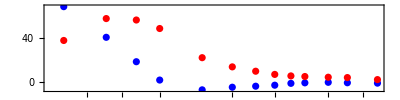

```mathematica
drudeBi=ListLogLinearPlot[{Style[biReal ,Blue],Style[biImag,Red]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],
FrameLabel->{{Style[MaTeX["\mbox{Re}[\epsilon (\omega)] "],Magnification->1.2],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.2],None}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{All,None},{Automatic,None}},PlotRange->All,AspectRatio->1/4]
```

```mathematica
Export["drudeBi.svg",drudeBi]
```

drudeBi.svg

```mathematica
h c/(5*10^(8))
```

2.4814×10^-6

```mathematica
upperTicks4=Module[{labels,positions},labels={2.5*^-6,3.1*^-6,4.1*^-6,6.2*^-6,1.24*10^(-5)};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor4=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

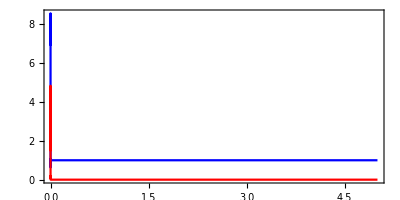

```mathematica
bis=ListLinePlot[{Style[Transpose[{ℏωBism,nBis}],Blue],Style[Transpose[{ℏωBism,kBis}],Red]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style[MaTeX["n,k"],Magnification->1.5],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.5],Style[MaTeX["\lambda[\mbox{nm}]"],Magnification->1.5]}},LabelStyle->{FontFamily->"CMU Serif",FontSize->20},FrameTicks->{{All,None},{Automatic,Join[upperTicksMinor4,upperTicks4]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,"CMU Serif",FontSize->20]&/@{MaTeX["n"],MaTeX["k "]}},LegendMarkerSize->15,LegendMargins->-0.1,Spacings->0.05],{0.85,0.65}],AspectRatio->1/2]
```

```mathematica
Export["Bisexp.svg",bis]
```

Bisexp.svg

### Óxido de magnesio

Datos obtenidos de Stephens and Malitson  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
mgO=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Óxido de magnesio Stephens.csv"];
```

```mathematica
mgO1=Drop[mgO,1];
λMgO=mgO1[[All,1]];(*λ en um*)
ℏωMgO=2 Pi c ℏ/λMgO; (*eV*)
nMgO=mgO1[[All,2]];
nmgo=Transpose[{λMgO,nMgO}];
```

```mathematica
hbarraomegaMgO=Drop[ℏωMgO,{1,2}];
epsRealMgO=Re[Drop[nMgO,{1,2}]^2];
epsImagMgO=Im[Drop[nMgO,{1,2}]^2];
```

```mathematica
auReal = Interpolation[Transpose[{hbarraomegaMgO,epsRealMgO}]];
auImag = Interpolation[Transpose[{hbarraomegaMgO,epsImagMgO}]];
```

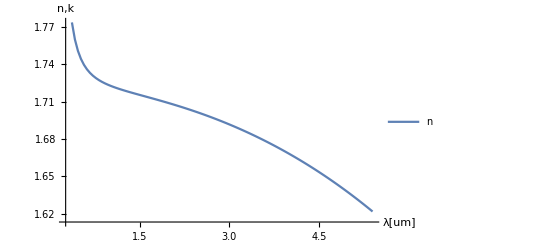

```mathematica
ListLinePlot[{Transpose[{λMgO,nMgO}]},PlotRange->All,AxesLabel->{"λ[um]","n,k"},PlotLegends->{"n"}]
```

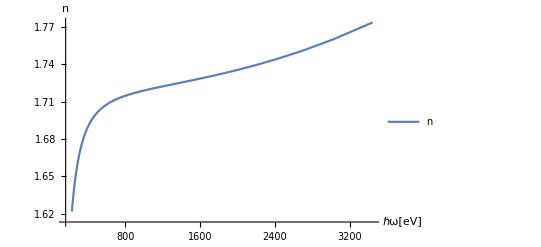

```mathematica
ListLinePlot[{Transpose[{ℏωMgO,nMgO}]},PlotRange->All,AxesLabel->{"ℏω[eV]","n"},PlotLegends->{"n","k"}]
```

### Aluminio

Datos obtenidos de Rakic.b4  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
alum=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Aluminio Rakic.csv"];
```

```mathematica
alum1=Drop[Drop[alum,{208,415}],1];
λalum=alum1[[All,1]];
ℏωalum=2 Pi c ℏ/λalum; (*eV*)
nalum=alum1[[All,2]];
alum2=Drop[alum,{1,209}];
kalum=alum2[[All,2]];
naluminio=nalum+ I kalum;
```

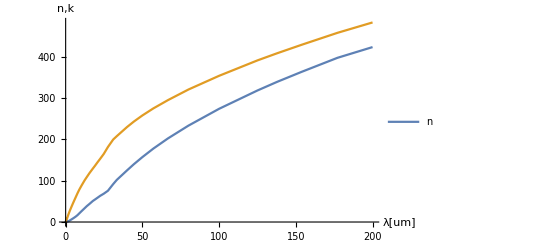

```mathematica
ListLinePlot[{Transpose[{λalum,nalum}],Transpose[{λalum,kalum}]},PlotRange->All,AxesLabel->{"λ[um]","n,k"},PlotLegends->{"n"}]
```

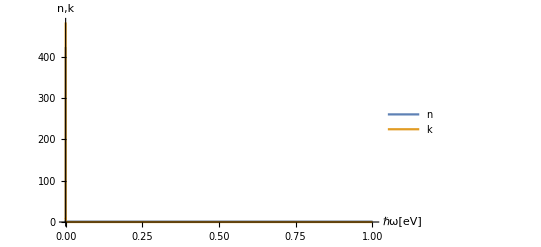

```mathematica
ListLinePlot[{Transpose[{ℏωalum,nalum}],Transpose[{ℏωalum,kalum}]},PlotRange->All,AxesLabel->{"ℏω[eV]","n,k"},PlotLegends->{"n","k"}]
```